```mathematica
Rre=MatrixExp[-I Ωe t/2 PauliMatrix[1]]
```

{{Cos[(t Ωe)/2],-ⅈ Sin[(t Ωe)/2]},{-ⅈ Sin[(t Ωe)/2],Cos[(t Ωe)/2]}}

```mathematica
Rg={{Cos[(t Ωg)/2]-ⅈ nz Sin[(t Ωg)/2],-(ⅈ nx+ny) Sin[(t Ωg)/2]},{(-ⅈ nx+ny) Sin[(t Ωg)/2],Cos[(t Ωg)/2]+ⅈ nz Sin[(t Ωg)/2]}}
```

{{Cos[(t Ωg)/2]-ⅈ nz Sin[(t Ωg)/2],(-ⅈ nx-ny) Sin[(t Ωg)/2]},{(-ⅈ nx+ny) Sin[(t Ωg)/2],Cos[(t Ωg)/2]+ⅈ nz Sin[(t Ωg)/2]}}

## We start from up, coherence and populations

```mathematica
fRupup=(({1,0}.Rg.{1,0})/.t->(T-t))Sqrt[γ]Exp[-γ t/2]({1,0}.Rre.{1,0})
```

(ⅇ^(-(t Γ)/4) √Γ Cos[(t Ωe)/2] (Cos[1/2 (-t+T) Ωg]-ⅈ nz Sin[1/2 (-t+T) Ωg]))/(√2)

```mathematica
fRupdwn=(({0,1}.Rg.{1,0})/.t->(T-t))Sqrt[γ]Exp[-γ t/2]({1,0}.Rre.{1,0})
```

(ⅇ^(-(t Γ)/4) (-ⅈ nx+ny) √Γ Cos[(t Ωe)/2] Sin[1/2 (-t+T) Ωg])/(√2)

```mathematica
coeRup=Integrate[fRupup*ⅇ^(-(t γ)/2) (ⅈ nx+ny) √γ Cos[(t Ωe)/2] Sin[((T-t) Ωg)/2],{t,0,T}]; (*il prodotto ha up come ket e dwn come bra*)
```

```mathematica
fLupup=(({1,0}.Rg.{0,1})/.t->(T-t))Sqrt[γ]Exp[-γ t/2]({0,1}.Rre.{1,0})
```

-(ⅈ ⅇ^(-(t Γ)/4) (-ⅈ nx-ny) √Γ Sin[(t Ωe)/2] Sin[1/2 (-t+T) Ωg])/(√2)

```mathematica
fLupdwn=(({0,1}.Rg.{0,1})/.t->(T-t))Sqrt[γ]Exp[-γ t/2]({0,1}.Rre.{1,0})
```

-(ⅈ ⅇ^(-(t Γ)/4) √Γ Sin[(t Ωe)/2] (Cos[1/2 (-t+T) Ωg]+ⅈ nz Sin[1/2 (-t+T) Ωg]))/(√2)

```mathematica
coeLup=Integrate[fLupup*(ⅈ ⅇ^(-(t γ)/2) √γ Sin[(t Ωe)/2] (Cos[((T-t) Ωg)/2]-ⅈ nz Sin[((T-t) Ωg)/2])),{t,0,T}];
```

```mathematica
normRupup=Integrate[ ((Cos[((T-t)Ωg)/2])^2+ nz^2( Sin[((T-t) Ωg)/2])^2)(Cos[((t)Ωe)/2])^2*γ Exp[-γ t],{t,0,T}];
```

```mathematica
normLupup=Integrate[(1-nz^2) ( Sin[((T-t) Ωg)/2])^2(Sin[((t)Ωe)/2])^2*γ Exp[-γ t],{t,0,T}];
```

```mathematica
normLupdwn=Integrate[ ((Cos[((T-t)Ωg)/2])^2+ nz^2( Sin[((T-t) Ωg)/2])^2)(Sin[((t)Ωe)/2])^2*γ Exp[-γ t],{t,0,T}];
```

```mathematica
normRupdwn=Integrate[(1-nz^2) ( Sin[((T-t) Ωg)/2])^2(Cos[((t)Ωe)/2])^2*γ Exp[-γ t],{t,0,T}];
```

```mathematica
coeup=coeLup+coeRup;
Pupup=normRupup+normLupup;
Pupdwn=normRupdwn+normLupdwn;
```

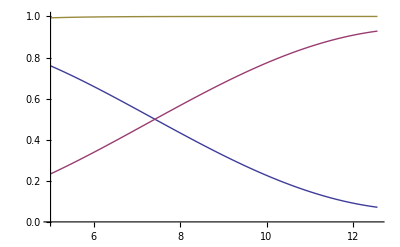

```mathematica
Plot[{Pupup/.{γ->1,nz->0.2,Ωg-> 0.25,Ωe->0.1},Pupdwn/.{γ->1,nz->0.2,Ωe->0.1,Ωg-> 0.25},(Pupup+Pupdwn)/.{γ->1,nz->0.2,Ωe->0.1,Ωg-> 0.25}},{T,5,Pi/0.25},GridLines->{{Pi,Pi/(0.5)},{0.5}}]
```

```mathematica
Exp[-Pi]//N
```

0.0432139

```mathematica
Im[coeup/.{Γ->2,nz->0,nx->Sqrt[1-(0.4)^2],ny->0.2,Ωg-> 0.5,Ωe->0.1}]
```

Im[(0.2+0.916515 ⅈ) (1/8 ⅇ^-T (0.8+0.215517 (1.6 Cos[0.1 T]-4 Sin[0.1 T])+0.183824 (2.4 Cos[0.1 T]+4 Sin[0.1 T]))+1/8 (0.-0.215517 (1.6 Cos[0.5 T]-4 Sin[0.5 T])-0.183824 (2.4 Cos[0.5 T]-4 Sin[0.5 T])-0.8 (1. Cos[0.5 T]-2 Sin[0.5 T])))-(0.916515-0.2 ⅈ) (1/8 ⅇ^-T ((0.+0.8 ⅈ)+ⅈ (0.183824 (-2.4 Cos[0.1 T]-4 Sin[0.1 T])-0.49505 (0.2 Cos[0.1 T]+2 Sin[0.1 T]))-ⅈ (0.215517 (1.6 Cos[0.1 T]-4 Sin[0.1 T])-0.49505 (0.2 Cos[0.1 T]+2 Sin[0.1 T])))+1/8 (0.+ⅈ (-0.0990099+0.215517 (1.6 Cos[0.5 T]-4 Sin[0.5 T]))-(0.+0.8 ⅈ) (1. Cos[0.5 T]-2 Sin[0.5 T])-ⅈ (-0.0990099+0.183824 (-2.4 Cos[0.5 T]+4 Sin[0.5 T]))))]

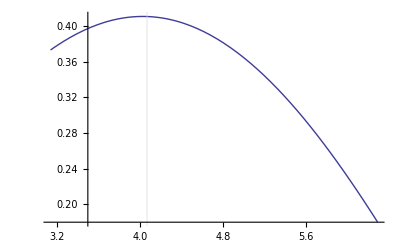

```mathematica
Plot[{ Im[coeup/.{Γ->2,nz->0,nx->Sqrt[1-(0.4)^2],ny->0.2,Ωg-> 0.5,Ωe->0.1}]},{T,Pi,Pi/0.5},GridLines->{{(Pi-ArcTan[Sqrt[1-(0.4)^2]/(Sqrt[1-(0.4)^2] 0.5)])/0.5},{0.5}}]
```

```mathematica
coeupltl=Simplify[coeup/.Exp[-γ T]->0.]
```

-((nx-ⅈ ny) Γ (-nz Γ (Γ^4+16 (Ωe^2-Ωg^2)^2+8 Γ^2 (Ωe^2+Ωg^2))+(Γ^2+4 Ωe^2) (2 ⅈ Ωg (Γ^2-4 Ωe^2+4 Ωg^2)+nz Γ (Γ^2+4 (Ωe^2+Ωg^2))) Cos[T Ωg]-ⅈ (Γ^2+4 Ωe^2) (Γ^3+2 ⅈ nz Γ^2 Ωg+8 ⅈ nz Ωg (-Ωe^2+Ωg^2)+4 Γ (Ωe^2+Ωg^2)) Sin[T Ωg]))/(2 (Γ^2+4 Ωe^2) (Γ^2+4 (Ωe-Ωg)^2) (Γ^2+4 (Ωe+Ωg)^2))

```mathematica
ComplexExpand[coeupltl]
```

(nx nz Γ^6)/(2 (Γ^2+4 Ωe^2) (Γ^2+4 (Ωe-Ωg)^2) (Γ^2+4 (Ωe+Ωg)^2))+(4 nx nz Γ^4 Ωe^2)/((Γ^2+4 Ωe^2) (Γ^2+4 (Ωe-Ωg)^2) (Γ^2+4 (Ωe+Ωg)^2))+(8 nx nz Γ^2 Ωe^4)/((Γ^2+4 Ωe^2) (Γ^2+4 (Ωe-Ωg)^2) (Γ^2+4 (Ωe+Ωg)^2))+(4 nx nz Γ^4 Ωg^2)/((Γ^2+4 Ωe^2) (Γ^2+4 (Ωe-Ωg)^2) (Γ^2+4 (Ωe+Ωg)^2))-(16 nx nz Γ^2 Ωe^2 Ωg^2)/((Γ^2+4 Ωe^2) (Γ^2+4 (Ωe-Ωg)^2) (Γ^2+4 (Ωe+Ωg)^2))+(8 nx nz Γ^2 Ωg^4)/((Γ^2+4 Ωe^2) (Γ^2+4 (Ωe-Ωg)^2) (Γ^2+4 (Ωe+Ωg)^2))-(nx nz Γ^6 Cos[T Ωg])/(2 (Γ^2+4 Ωe^2) (Γ^2+4 (Ωe-Ωg)^2) (Γ^2+4 (Ωe+Ωg)^2))-(4 nx nz Γ^4 Ωe^2 Cos[T Ωg])/((Γ^2+4 Ωe^2) (Γ^2+4 (Ωe-Ωg)^2) (Γ^2+4 (Ωe+Ωg)^2))-(8 nx nz Γ^2 Ωe^4 Cos[T Ωg])/((Γ^2+4 Ωe^2) (Γ^2+4 (Ωe-Ωg)^2) (Γ^2+4 (Ωe+Ωg)^2))-(ny Γ^5 Ωg Cos[T Ωg])/((Γ^2+4 Ωe^2) (Γ^2+4 (Ωe-Ωg)^2) (Γ^2+4 (Ωe+Ωg)^2))+(16 ny Γ Ωe^4 Ωg Cos[T Ωg])/((Γ^2+4 Ωe^2) (Γ^2+4 (Ωe-Ωg)^2) (Γ^2+4 (Ωe+Ωg)^2))-(2 nx nz Γ^4 Ωg^2 Cos[T Ωg])/((Γ^2+4 Ωe^2) (Γ^2+4 (Ωe-Ωg)^2) (Γ^2+4 (Ωe+Ωg)^2))-(8 nx nz Γ^2 Ωe^2 Ωg^2 Cos[T Ωg])/((Γ^2+4 Ωe^2) (Γ^2+4 (Ωe-Ωg)^2) (Γ^2+4 (Ωe+Ωg)^2))-(4 ny Γ^3 Ωg^3 Cos[T Ωg])/((Γ^2+4 Ωe^2) (Γ^2+4 (Ωe-Ωg)^2) (Γ^2+4 (Ωe+Ωg)^2))-(16 ny Γ Ωe^2 Ωg^3 Cos[T Ωg])/((Γ^2+4 Ωe^2) (Γ^2+4 (Ωe-Ωg)^2) (Γ^2+4 (Ωe+Ωg)^2))+(ny Γ^6 Sin[T Ωg])/(2 (Γ^2+4 Ωe^2) (Γ^2+4 (Ωe-Ωg)^2) (Γ^2+4 (Ωe+Ωg)^2))+(4 ny Γ^4 Ωe^2 Sin[T Ωg])/((Γ^2+4 Ωe^2) (Γ^2+4 (Ωe-Ωg)^2) (Γ^2+4 (Ωe+Ωg)^2))+(8 ny Γ^2 Ωe^4 Sin[T Ωg])/((Γ^2+4 Ωe^2) (Γ^2+4 (Ωe-Ωg)^2) (Γ^2+4 (Ωe+Ωg)^2))-(nx nz Γ^5 Ωg Sin[T Ωg])/((Γ^2+4 Ωe^2) (Γ^2+4 (Ωe-Ωg)^2) (Γ^2+4 (Ωe+Ωg)^2))+(16 nx nz Γ Ωe^4 Ωg Sin[T Ωg])/((Γ^2+4 Ωe^2) (Γ^2+4 (Ωe-Ωg)^2) (Γ^2+4 (Ωe+Ωg)^2))+(2 ny Γ^4 Ωg^2 Sin[T Ωg])/((Γ^2+4 Ωe^2) (Γ^2+4 (Ωe-Ωg)^2) (Γ^2+4 (Ωe+Ωg)^2))+(8 ny Γ^2 Ωe^2 Ωg^2 Sin[T Ωg])/((Γ^2+4 Ωe^2) (Γ^2+4 (Ωe-Ωg)^2) (Γ^2+4 (Ωe+Ωg)^2))-(4 nx nz Γ^3 Ωg^3 Sin[T Ωg])/((Γ^2+4 Ωe^2) (Γ^2+4 (Ωe-Ωg)^2) (Γ^2+4 (Ωe+Ωg)^2))-(16 nx nz Γ Ωe^2 Ωg^3 Sin[T Ωg])/((Γ^2+4 Ωe^2) (Γ^2+4 (Ωe-Ωg)^2) (Γ^2+4 (Ωe+Ωg)^2))+ⅈ (-(ny nz Γ^6)/(2 (Γ^2+4 Ωe^2) (Γ^2+4 (Ωe-Ωg)^2) (Γ^2+4 (Ωe+Ωg)^2))-(4 ny nz Γ^4 Ωe^2)/((Γ^2+4 Ωe^2) (Γ^2+4 (Ωe-Ωg)^2) (Γ^2+4 (Ωe+Ωg)^2))-(8 ny nz Γ^2 Ωe^4)/((Γ^2+4 Ωe^2) (Γ^2+4 (Ωe-Ωg)^2) (Γ^2+4 (Ωe+Ωg)^2))-(4 ny nz Γ^4 Ωg^2)/((Γ^2+4 Ωe^2) (Γ^2+4 (Ωe-Ωg)^2) (Γ^2+4 (Ωe+Ωg)^2))+(16 ny nz Γ^2 Ωe^2 Ωg^2)/((Γ^2+4 Ωe^2) (Γ^2+4 (Ωe-Ωg)^2) (Γ^2+4 (Ωe+Ωg)^2))-(8 ny nz Γ^2 Ωg^4)/((Γ^2+4 Ωe^2) (Γ^2+4 (Ωe-Ωg)^2) (Γ^2+4 (Ωe+Ωg)^2))+(ny nz Γ^6 Cos[T Ωg])/(2 (Γ^2+4 Ωe^2) (Γ^2+4 (Ωe-Ωg)^2) (Γ^2+4 (Ωe+Ωg)^2))+(4 ny nz Γ^4 Ωe^2 Cos[T Ωg])/((Γ^2+4 Ωe^2) (Γ^2+4 (Ωe-Ωg)^2) (Γ^2+4 (Ωe+Ωg)^2))+(8 ny nz Γ^2 Ωe^4 Cos[T Ωg])/((Γ^2+4 Ωe^2) (Γ^2+4 (Ωe-Ωg)^2) (Γ^2+4 (Ωe+Ωg)^2))-(nx Γ^5 Ωg Cos[T Ωg])/((Γ^2+4 Ωe^2) (Γ^2+4 (Ωe-Ωg)^2) (Γ^2+4 (Ωe+Ωg)^2))+(16 nx Γ Ωe^4 Ωg Cos[T Ωg])/((Γ^2+4 Ωe^2) (Γ^2+4 (Ωe-Ωg)^2) (Γ^2+4 (Ωe+Ωg)^2))+(2 ny nz Γ^4 Ωg^2 Cos[T Ωg])/((Γ^2+4 Ωe^2) (Γ^2+4 (Ωe-Ωg)^2) (Γ^2+4 (Ωe+Ωg)^2))+(8 ny nz Γ^2 Ωe^2 Ωg^2 Cos[T Ωg])/((Γ^2+4 Ωe^2) (Γ^2+4 (Ωe-Ωg)^2) (Γ^2+4 (Ωe+Ωg)^2))-(4 nx Γ^3 Ωg^3 Cos[T Ωg])/((Γ^2+4 Ωe^2) (Γ^2+4 (Ωe-Ωg)^2) (Γ^2+4 (Ωe+Ωg)^2))-(16 nx Γ Ωe^2 Ωg^3 Cos[T Ωg])/((Γ^2+4 Ωe^2) (Γ^2+4 (Ωe-Ωg)^2) (Γ^2+4 (Ωe+Ωg)^2))+(nx Γ^6 Sin[T Ωg])/(2 (Γ^2+4 Ωe^2) (Γ^2+4 (Ωe-Ωg)^2) (Γ^2+4 (Ωe+Ωg)^2))+(4 nx Γ^4 Ωe^2 Sin[T Ωg])/((Γ^2+4 Ωe^2) (Γ^2+4 (Ωe-Ωg)^2) (Γ^2+4 (Ωe+Ωg)^2))+(8 nx Γ^2 Ωe^4 Sin[T Ωg])/((Γ^2+4 Ωe^2) (Γ^2+4 (Ωe-Ωg)^2) (Γ^2+4 (Ωe+Ωg)^2))+(ny nz Γ^5 Ωg Sin[T Ωg])/((Γ^2+4 Ωe^2) (Γ^2+4 (Ωe-Ωg)^2) (Γ^2+4 (Ωe+Ωg)^2))-(16 ny nz Γ Ωe^4 Ωg Sin[T Ωg])/((Γ^2+4 Ωe^2) (Γ^2+4 (Ωe-Ωg)^2) (Γ^2+4 (Ωe+Ωg)^2))+(2 nx Γ^4 Ωg^2 Sin[T Ωg])/((Γ^2+4 Ωe^2) (Γ^2+4 (Ωe-Ωg)^2) (Γ^2+4 (Ωe+Ωg)^2))+(8 nx Γ^2 Ωe^2 Ωg^2 Sin[T Ωg])/((Γ^2+4 Ωe^2) (Γ^2+4 (Ωe-Ωg)^2) (Γ^2+4 (Ωe+Ωg)^2))+(4 ny nz Γ^3 Ωg^3 Sin[T Ωg])/((Γ^2+4 Ωe^2) (Γ^2+4 (Ωe-Ωg)^2) (Γ^2+4 (Ωe+Ωg)^2))+(16 ny nz Γ Ωe^2 Ωg^3 Sin[T Ωg])/((Γ^2+4 Ωe^2) (Γ^2+4 (Ωe-Ωg)^2) (Γ^2+4 (Ωe+Ωg)^2)))

```mathematica
(nx nz γ^6)/(2 (γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))+(nx nz γ^4 Ωe^2)/((γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))+(nx nz γ^2 Ωe^4)/(2 (γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))+(nx nz γ^4 Ωg^2)/((γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))-(nx nz γ^2 Ωe^2 Ωg^2)/((γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))+(nx nz γ^2 Ωg^4)/(2 (γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))-(nx nz γ^6 Cos[T Ωg])/(2 (γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))-(nx nz γ^4 Ωe^2 Cos[T Ωg])/((γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))-(nx nz γ^2 Ωe^4 Cos[T Ωg])/(2 (γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))-(ny γ^5 Ωg Cos[T Ωg])/(2 (γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))+(ny γ Ωe^4 Ωg Cos[T Ωg])/(2 (γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))-(nx nz γ^4 Ωg^2 Cos[T Ωg])/(2 (γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))-(nx nz γ^2 Ωe^2 Ωg^2 Cos[T Ωg])/(2 (γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))-(ny γ^3 Ωg^3 Cos[T Ωg])/(2 (γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))-(ny γ Ωe^2 Ωg^3 Cos[T Ωg])/(2 (γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))+(ny γ^6 Sin[T Ωg])/(2 (γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))+(ny γ^4 Ωe^2 Sin[T Ωg])/((γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))+(ny γ^2 Ωe^4 Sin[T Ωg])/(2 (γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))-(nx nz γ^5 Ωg Sin[T Ωg])/(2 (γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))+(nx nz γ Ωe^4 Ωg Sin[T Ωg])/(2 (γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))+(ny γ^4 Ωg^2 Sin[T Ωg])/(2 (γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))+(ny γ^2 Ωe^2 Ωg^2 Sin[T Ωg])/(2 (γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))-(nx nz γ^3 Ωg^3 Sin[T Ωg])/(2 (γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))-(nx nz γ Ωe^2 Ωg^3 Sin[T Ωg])/(2 (γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))+ⅈ
```

```mathematica
Imcoeh=((nx γ^6)/(2 (γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))-(ny nz γ^6)/(2 (γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))+(nx γ^4 Ωe^2)/((γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))-(ny nz γ^4 Ωe^2)/((γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))+(nx γ^2 Ωe^4)/(2 (γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))-(ny nz γ^2 Ωe^4)/(2 (γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))+(ny nz γ^5 Ωg)/(2 (γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))-(ny nz γ Ωe^4 Ωg)/(2 (γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))+(nx γ^4 Ωg^2)/(2 (γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))-(ny nz γ^4 Ωg^2)/((γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))+(nx γ^2 Ωe^2 Ωg^2)/(2 (γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))+(ny nz γ^2 Ωe^2 Ωg^2)/((γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))+(ny nz γ^3 Ωg^3)/(2 (γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))+(ny nz γ Ωe^2 Ωg^3)/(2 (γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))-(ny nz γ^2 Ωg^4)/(2 (γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2)))//Simplify;
```

```mathematica
(γ (nx γ (γ^2+Ωe^2) (γ^2+Ωe^2+Ωg^2)-ny nz (γ^5-γ^4 Ωg-γ^2 Ωg^3+Ωe^2 Ωg (Ωe^2-Ωg^2)+γ (Ωe^2-Ωg^2)^2+2 γ^3 (Ωe^2+Ωg^2))))/(2 (γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))
```

```mathematica
fyz=(γ (γ^5-γ^4 Ωg-γ^2 Ωg^3+Ωe^2 Ωg (Ωe^2-Ωg^2)+γ (Ωe^2-Ωg^2)^2+2 γ^3 (Ωe^2+Ωg^2)))/(2 (γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))//FullSimplify
```

1/4 γ ((2 γ)/(γ^2+Ωe^2)+(Ωe-Ωg)/(γ^2+(Ωe-Ωg)^2)-(Ωe+Ωg)/(γ^2+(Ωe+Ωg)^2))

```mathematica
Fidelity=(-(ny nz γ^6)/(2 (γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))-(ny nz γ^4 Ωe^2)/((γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))-(ny nz γ^2 Ωe^4)/(2 (γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))-(ny nz γ^4 Ωg^2)/((γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))+(ny nz γ^2 Ωe^2 Ωg^2)/((γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))-(ny nz γ^2 Ωg^4)/(2 (γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))+(ny nz γ^6 Cos[T Ωg])/(2 (γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))+(ny nz γ^4 Ωe^2 Cos[T Ωg])/((γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))+(ny nz γ^2 Ωe^4 Cos[T Ωg])/(2 (γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))-(nx γ^5 Ωg Cos[T Ωg])/(2 (γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))+(nx γ Ωe^4 Ωg Cos[T Ωg])/(2 (γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))+(ny nz γ^4 Ωg^2 Cos[T Ωg])/(2 (γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))+(ny nz γ^2 Ωe^2 Ωg^2 Cos[T Ωg])/(2 (γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))-(nx γ^3 Ωg^3 Cos[T Ωg])/(2 (γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))-(nx γ Ωe^2 Ωg^3 Cos[T Ωg])/(2 (γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))+(nx γ^6 Sin[T Ωg])/(2 (γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))+(nx γ^4 Ωe^2 Sin[T Ωg])/((γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))+(nx γ^2 Ωe^4 Sin[T Ωg])/(2 (γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))+(ny nz γ^5 Ωg Sin[T Ωg])/(2 (γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))-(ny nz γ Ωe^4 Ωg Sin[T Ωg])/(2 (γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))+(nx γ^4 Ωg^2 Sin[T Ωg])/(2 (γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))+(nx γ^2 Ωe^2 Ωg^2 Sin[T Ωg])/(2 (γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))+(ny nz γ^3 Ωg^3 Sin[T Ωg])/(2 (γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))+(ny nz γ Ωe^2 Ωg^3 Sin[T Ωg])/(2 (γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2)))/.γ->1//Simplify
```

(-ny nz (Ωe^4-2 Ωe^2 (-1+Ωg^2)+(1+Ωg^2)^2)+(1+Ωe^2) (nx Ωg (-1+Ωe^2-Ωg^2)+ny nz (1+Ωe^2+Ωg^2)) Cos[T Ωg]+(1+Ωe^2) (ny nz Ωg (1-Ωe^2+Ωg^2)+nx (1+Ωe^2+Ωg^2)) Sin[T Ωg])/(2 (1+Ωe^2) (1+Ωe^2-2 Ωe Ωg+Ωg^2) (1+Ωe^2+2 Ωe Ωg+Ωg^2))

```mathematica
approxf=Fidelity/.{Ωe^2->0,Ωg^2->0,Ωe Ωg->0,Ωe^4->0}
```

1/2 (-ny nz+(ny nz-nx Ωg) Cos[T Ωg]+(nx+ny nz Ωg) Sin[T Ωg])

```mathematica
sol=Solve[D[approxf,T]==0,T]
```

{{T→ConditionalExpression[(ArcTan[-(ny nz-nx Ωg)/(√(nx^2+ny^2 nz^2+nx^2 Ωg^2+ny^2 nz^2 Ωg^2)),((nx ny nz)/(√((nx^2+ny^2 nz^2) (1+Ωg^2)))-(nx^2 Ωg)/(√((nx^2+ny^2 nz^2) (1+Ωg^2)))+(ny^2 nz^2 Ωg)/(√((nx^2+ny^2 nz^2) (1+Ωg^2)))-(nx ny nz Ωg^2)/(√((nx^2+ny^2 nz^2) (1+Ωg^2))))/(-ny nz+nx Ωg)]+2 π C[1])/Ωg,C[1]∈Integers]},{T→ConditionalExpression[(ArcTan[(ny nz-nx Ωg)/(√(nx^2+ny^2 nz^2+nx^2 Ωg^2+ny^2 nz^2 Ωg^2)),(-(nx ny nz)/(√((nx^2+ny^2 nz^2) (1+Ωg^2)))+(nx^2 Ωg)/(√((nx^2+ny^2 nz^2) (1+Ωg^2)))-(ny^2 nz^2 Ωg)/(√((nx^2+ny^2 nz^2) (1+Ωg^2)))+(nx ny nz Ωg^2)/(√((nx^2+ny^2 nz^2) (1+Ωg^2))))/(-ny nz+nx Ωg)]+2 π C[1])/Ωg,C[1]∈Integers]}}

```mathematica
T/.sol/.{nx^2ny^2->0,nx^2nz^2->0,nz^2ny^2->0}
```

{ConditionalExpression[(ArcTan[-(ny nz-nx Ωg)/(√(nx^2+nx^2 Ωg^2)),((nx ny nz)/(√(nx^2 (1+Ωg^2)))-(nx^2 Ωg)/(√(nx^2 (1+Ωg^2)))-(nx ny nz Ωg^2)/(√(nx^2 (1+Ωg^2))))/(-ny nz+nx Ωg)]+2 π C[1])/Ωg,C[1]∈Integers],ConditionalExpression[(ArcTan[(ny nz-nx Ωg)/(√(nx^2+nx^2 Ωg^2)),(-(nx ny nz)/(√(nx^2 (1+Ωg^2)))+(nx^2 Ωg)/(√(nx^2 (1+Ωg^2)))+(nx ny nz Ωg^2)/(√(nx^2 (1+Ωg^2))))/(-ny nz+nx Ωg)]+2 π C[1])/Ωg,C[1]∈Integers]}

```mathematica
trial=ArcTan[-(ny nz-nx Ωg)/(√(nx^2+nx^2 Ωg^2)),((nx ny nz)/(√(nx^2 (1+Ωg^2)))-(nx^2 Ωg)/(√(nx^2 (1+Ωg^2)))-(nx ny nz Ωg^2)/(√(nx^2 (1+Ωg^2))))/(-ny nz+nx Ωg)]/Ωg//FullSimplify
```

ArcTan[(-ny nz+nx Ωg)/(√(nx^2 (1+Ωg^2))),-(nx (nx Ωg+ny nz (-1+Ωg^2)))/((-ny nz+nx Ωg) √(nx^2 (1+Ωg^2)))]/Ωg

```mathematica
Fidelity/.{T->Pi/Ωg-ArcTan[nx/(nx Ωg-ny nz)]/Ωg}
```

(-ny nz (Ωe^4-2 Ωe^2 (-1+Ωg^2)+(1+Ωg^2)^2)+(1+Ωe^2) (nx Ωg (-1+Ωe^2-Ωg^2)+ny nz (1+Ωe^2+Ωg^2)) Cos[Ωg (π/Ωg-ArcTan[nx/(-ny nz+nx Ωg)]/Ωg)]+(1+Ωe^2) (ny nz Ωg (1-Ωe^2+Ωg^2)+nx (1+Ωe^2+Ωg^2)) Sin[Ωg (π/Ωg-ArcTan[nx/(-ny nz+nx Ωg)]/Ωg)])/(2 (1+Ωe^2) (1+Ωe^2-2 Ωe Ωg+Ωg^2) (1+Ωe^2+2 Ωe Ωg+Ωg^2))

## We start from down, coherence and populations

```mathematica
fRdwnup=(({1,0}.Rg.{1,0})/.t->(T-t))Sqrt[γ]Exp[-γ t/2]({1,0}.Rre.{0,1})
```

-ⅈ ⅇ^(-(t γ)/2) √γ Sin[(t Ωe)/2] (Cos[1/2 (-t+T) Ωg]-ⅈ nz Sin[1/2 (-t+T) Ωg])

```mathematica
fRdwndwn=(({0,1}.Rg.{1,0})/.t->(T-t))Sqrt[γ]Exp[-γ t/2]({1,0}.Rre.{0,1})
```

-ⅈ ⅇ^(-(t γ)/2) (-ⅈ nx+ny) √γ Sin[(t Ωe)/2] Sin[1/2 (-t+T) Ωg]

```mathematica
coeRdwn=Integrate[fRdwnup*(ⅈ ⅇ^(-(t γ)/2) (ⅈ nx+ny) √γ Sin[(t Ωe)/2] Sin[1/2 (-t+T) Ωg]),{t,0,T}]; (*il prodotto ha up come ket e dwn come bra*)
```

```mathematica
fLdwnup=(({1,0}.Rg.{0,1})/.t->(T-t))Sqrt[γ]Exp[-γ t/2]({0,1}.Rre.{0,1})
```

ⅇ^(-(t γ)/2) (-ⅈ nx-ny) √γ Cos[(t Ωe)/2] Sin[1/2 (-t+T) Ωg]

```mathematica
fLdwndwn=(({0,1}.Rg.{0,1})/.t->(T-t))Sqrt[γ]Exp[-γ t/2]({0,1}.Rre.{0,1})
```

ⅇ^(-(t γ)/2) √γ Cos[(t Ωe)/2] (Cos[1/2 (-t+T) Ωg]+ⅈ nz Sin[1/2 (-t+T) Ωg])

```mathematica
coeLdwn=Integrate[fLdwnup*(ⅇ^(-(t γ)/2) √γ Cos[(t Ωe)/2] (Cos[1/2 (-t+T) Ωg]-ⅈ nz Sin[1/2 (-t+T) Ωg])),{t,0,T}];
```

```mathematica
normLdwndwn=Integrate[ ((Cos[((T-t)Ωg)/2])^2+ nz^2( Sin[((T-t) Ωg)/2])^2)(Cos[((t)Ωe)/2])^2*γ Exp[-γ t],{t,0,T}];
```

```mathematica
normLdwnup=Integrate[(1-nz^2) ( Sin[((T-t) Ωg)/2])^2(Cos[((t)Ωe)/2])^2*γ Exp[-γ t],{t,0,T}];
```

```mathematica
normRdwnup=Integrate[ ((Cos[((T-t)Ωg)/2])^2+ nz^2( Sin[((T-t) Ωg)/2])^2)(Sin[((t)Ωe)/2])^2*γ Exp[-γ t],{t,0,T}];
```

```mathematica
normRdwndwn=Integrate[(1-nz^2) ( Sin[((T-t) Ωg)/2])^2(Sin[((t)Ωe)/2])^2*γ Exp[-γ t],{t,0,T}];
```

```mathematica
coedwn=coeLdwn+coeRdwn;
Pdwnup=normLdwnup+normRdwnup;
Pdwndwn=normRdwndwn+normLdwndwn;
```

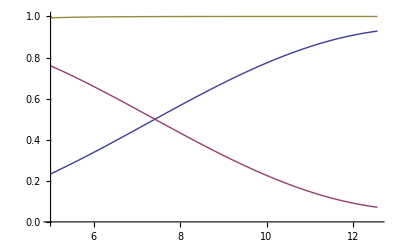

```mathematica
Plot[{Pdwnup/.{γ->1,nz->0.2,Ωg-> 0.25,Ωe->0.1},Pdwndwn/.{γ->1,nz->0.2,Ωe->0.1,Ωg-> 0.25},(Pdwnup+Pdwndwn)/.{γ->1,nz->0.2,Ωe->0.1,Ωg-> 0.25}},{T,5,Pi/0.25},GridLines->{{Pi,Pi/(0.5)},{0.5}}]
```

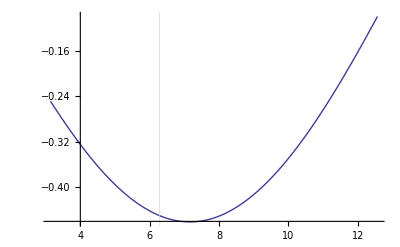

```mathematica
Plot[{ Im[coedwn/.{γ->1,nz->0.,nx->Sqrt[(1-(0.)^2)],ny->0,Ωg-> 0.25,Ωe->0.25}]},{T,Pi,Pi/(0.25)},GridLines->{{Pi/(0.5)},{0.5}}]
```

## Bhata coeff

```mathematica
leading=(Pupup/.T->(Pi/(2Ωg)))*Conjugate[(coeup/.T-> (τ-Pi/(2Ωg)))]+ (Pupdwn/.T->(Pi/(2Ωg)))*Conjugate[coedwn/.T-> (τ-Pi/(2Ωg))];
```

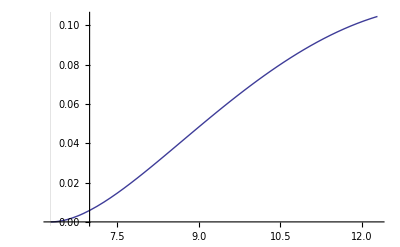

```mathematica
Plot[ Abs[leading/.{γ->1,nz->0.,nx->Sqrt[(1-(0.)^2)],ny->0,Ωg-> 0.25,Ωe->0.1}],{τ,Pi/0.5,Pi/0.5+6},GridLines->{{Pi/(0.5)},{0.5}}]
```

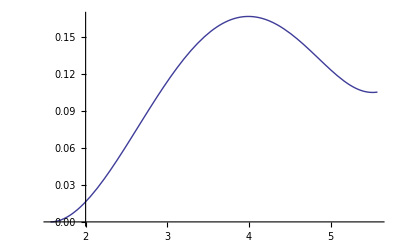

```mathematica
Plot[ Abs[leading/.{γ->1,nz->0.3,nx->Sqrt[(1-(0.3)^2-(0.3)^2)],ny->0.3,Ωg->1.,Ωe->0.02}],{τ,(Pi/2),(Pi/2)+4},GridLines->{{Pi/(0.5)},{0.5}}]
```

```mathematica
OuuddR=Integrate[ fRupup(ⅈ ⅇ^(-(t γ)/2) (ⅈ nx+ny) √γ Sin[(t Ωe)/2] Sin[1/2 (-t+T) Ωg]),{t,0,T}];
```

```mathematica
OuuddL=Integrate[ fLupup ⅇ^(-(t γ)/2) √γ Cos[(t Ωe)/2] (Cos[1/2 (-t+T) Ωg]-ⅈ nz Sin[1/2 (-t+T) Ωg]),{t,0,T}];
```

```mathematica
OduudR=Integrate[ fRdwnup ⅇ^(-(t γ)/2) (ⅈ nx+ny) √γ Cos[(t Ωe)/2] Sin[1/2 (-t+T) Ωg],{t,0,T}];
```

```mathematica
OduudL=Integrate[ fLdwnup (ⅈ ⅇ^(-(t γ)/2) √γ Sin[(t Ωe)/2] (Cos[1/2 (-t+T) Ωg]-ⅈ nz Sin[1/2 (-t+T) Ωg])),{t,0,T}];
```

```mathematica
subleadin=Conjugate[(coeup/.T->Pi/(2Ωg))]*(OuuddR+OuuddL)/.T->(τ-Pi/(2Ωg))+(coeup/.T->Pi/(2Ωg))*(OduudR+OduudL)/.T->(τ-Pi/(2Ωg));
```

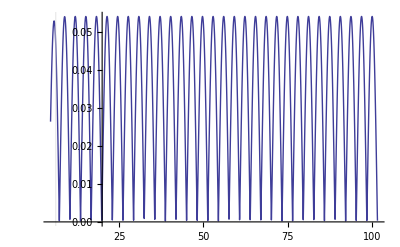

```mathematica
Plot[ Abs[(leading+subleadin)/.{γ->1,nz->0.,nx->1.,ny->0.,Ωg->1,Ωe->1}],{τ,(Pi/2)+Pi,(Pi/2)+100},GridLines->{{Pi/(0.5)},{0.5}}]
```

```mathematica
OR=Integrate[ fRupup*Sqrt[γ] Exp[-γ t/2],{t,0,T}]
```

(2 ⅇ^(-T γ) γ (-(8 γ^3+4 ⅈ nz γ^2 Ωg+ⅈ nz Ωg (-Ωe^2+Ωg^2)+2 γ (Ωe^2+Ωg^2)) Cos[(T Ωe)/2]+ⅇ^(T γ) (8 γ^3+4 ⅈ nz γ^2 Ωg+ⅈ nz Ωg (-Ωe^2+Ωg^2)+2 γ (Ωe^2+Ωg^2)) Cos[(T Ωg)/2]+Ωe (4 γ^2+Ωe^2+4 ⅈ nz γ Ωg-Ωg^2) Sin[(T Ωe)/2]+ⅇ^(T γ) (Ωg (4 γ^2-Ωe^2+Ωg^2)-2 ⅈ nz γ (4 γ^2+Ωe^2+Ωg^2)) Sin[(T Ωg)/2]))/((4 γ^2+(Ωe-Ωg)^2) (4 γ^2+(Ωe+Ωg)^2))

```mathematica
Abs[OR/.{nz->0,γ->1,Ωe->Ωg}]^2
```

1/4 ⅇ^(-2 Re[T]) Abs[1/(4+4 Ωg^2)(-(8+4 Ωg^2) Cos[(T Ωg)/2]+ⅇ^T (8+4 Ωg^2) Cos[(T Ωg)/2]+4 Ωg Sin[(T Ωg)/2]+4 ⅇ^T Ωg Sin[(T Ωg)/2])]^2

```mathematica
PupTm=(normRupup+normLupup)/.T->Pi/(2Ωg) //Simplify;
```

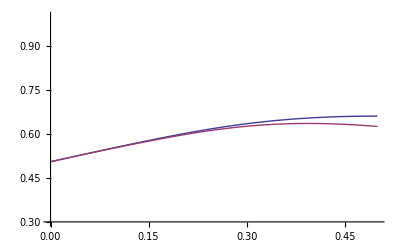

```mathematica
Plot[{PupTm/.{nz->0.1,γ->1,Ωe->Ωg/4},Abs[OR/.{nz->0.1,γ->1,Ωe->Ωg/4,T->Pi/(2Ωg)}]^2},{Ωg,0.,0.5},PlotRange->{0.3,1}]
```

```mathematica
IRup=((Cos[((T-t)Ωg)/2])^2+ nz^2( Sin[((T-t) Ωg)/2])^2)(Cos[((t)Ωe)/2])^2*γ Exp[-γ t]+(Sin[((T-t)Ωg)/2])^2 (1-nz^2)(Cos[((t)Ωe)/2])^2*γ Exp[-γ t];
```

```mathematica
Manipulate[Plot[IRup/.{Ωe->3,Ωg->3.,nz->0.5,γ->1.,T->p},{t, 0,10},PlotRange->All],{p,10,50,2}]
```

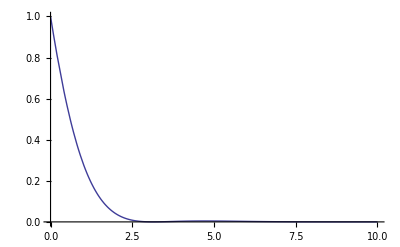

```mathematica
Plot[IRup/.{Ωe->1,Ωg->1,nz->0.5,γ->1.,T->20},{t, 0,10},PlotRange->All]
```

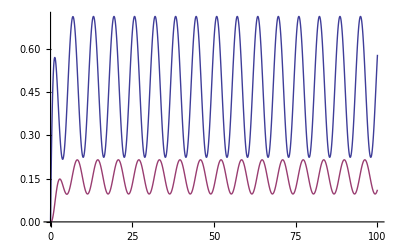

```mathematica
Plot[{normRupup/.{Ωe->1,Ωg->1,nz->0.5,γ->1.},normLupup/.{Ωe->1,Ωg->1,nz->0.5,γ->1.}},{T, 0,100},PlotRange->All]
```

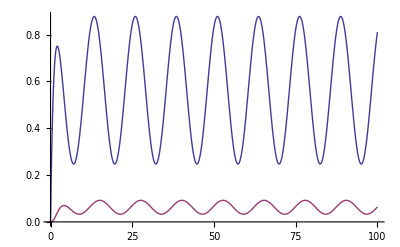

```mathematica
Plot[{normRupup/.{Ωe->0.5,Ωg->0.5,nz->0.5,γ->1.},normLupup/.{Ωe->0.5,Ωg->0.5,nz->0.5,γ->1.}},{T, 0,100},PlotRange->All]
```

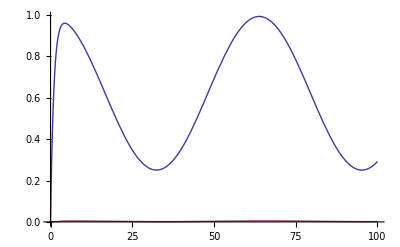

```mathematica
Plot[{normRupup/.{Ωe->0.1,Ωg->0.1,nz->0.5,γ->1.},normLupup/.{Ωe->0.1,Ωg->0.1,nz->0.5,γ->1.}},{T, 0,100},PlotRange->All]
```

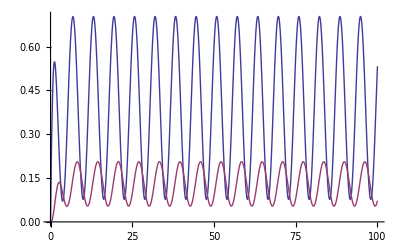

```mathematica
Plot[{normRupup/.{Ωe->1.,Ωg->1,nz->0.2,γ->1.},normLupup/.{Ωe->1,Ωg->1,nz->0.2,γ->1.}},{T, 0,100},PlotRange->All]
```

```mathematica
normLupdwn=Integrate[ (Sin[((T-t)Ωg)/2])^2 (1-nz^2)(Sin[((t)Ωe)/2])^2*γ Exp[-γ t],{t,0,T}];
```

```mathematica
normRupdwn=Integrate[ (Sin[((T-t)Ωg)/2])^2 (1-nz^2)(Cos[((t)Ωe)/2])^2*γ Exp[-γ t],{t,0,T}];
```

```mathematica
(0.5)^4
```

0.0625

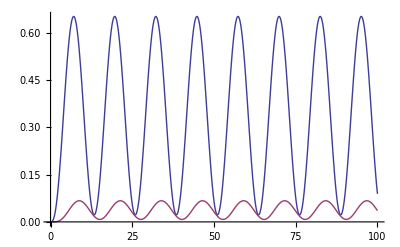

```mathematica
Plot[{normRupdwn/.{Ωe->0.5,Ωg->0.5,nz->0.5,γ->1.},normLupdwn/.{Ωe->0.5,Ωg->0.5,nz->0.5,γ->1.}},{T, 0,100},PlotRange->All]
```

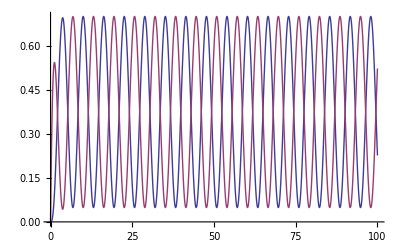

```mathematica
Plot[{normRupdwn/.{Ωe->1.,Ωg->1.,nz->0.,γ->1.},normRupup/.{Ωe->1.,Ωg->1.,nz->0.,γ->1.}},{T, 0,100},PlotRange->All]
```

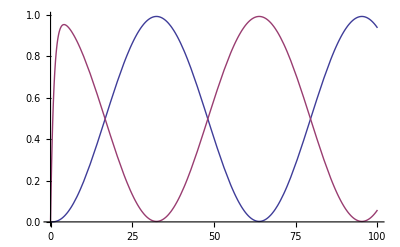

```mathematica
Plot[{normRupdwn/.{Ωe->0.1,Ωg->0.1,nz->0.,γ->1.},normRupup/.{Ωe->0.1,Ωg->0.1,nz->0.,γ->1.}},{T, 0,100},PlotRange->All]
```

```mathematica
Plot[{normRupdwn/.{Ωe->0.1,Ωg->0.1,nz->0.,γ->1.},normRupup/.{Ωe->0.1,Ωg->0.1,nz->0.,γ->1.}},{T, 0,100},PlotRange->All]
```

-Graphics-

```mathematica
σminUp=Integrate[γ Exp[-γ t](Cos[((T-t) Ωg)/2]-ⅈ nz Sin[((T-t) Ωg)/2])* (ⅈ nx+ny) Sin[((T-t) Ωg)/2]Cos[t Ωe],{t,0,T}]//Simplify
```

1/4 (ⅈ nx+ny) γ ((2 ⅇ^(-T γ) Ωg ((γ^4-Ωe^4+ⅈ nz γ^3 Ωg+γ^2 Ωg^2+Ωe^2 Ωg^2+ⅈ nz γ Ωg (-3 Ωe^2+Ωg^2)) Cos[T Ωe]-Ωe (2 γ^3+2 γ Ωe^2+3 ⅈ nz γ^2 Ωg+ⅈ nz Ωg (-Ωe^2+Ωg^2)) Sin[T Ωe]))/((γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))+((Ωe-Ωg) Cos[T Ωg]+γ Sin[T Ωg])/(γ^2+(Ωe-Ωg)^2)+(-(Ωe+Ωg) Cos[T Ωg]+γ Sin[T Ωg])/(γ^2+(Ωe+Ωg)^2)+ⅈ nz (-γ/(γ^2+Ωe^2)+(γ Cos[T Ωg]+(-Ωe+Ωg) Sin[T Ωg])/(γ^2+(Ωe-Ωg)^2))-ⅈ nz (γ/(γ^2+Ωe^2)-(γ Cos[T Ωg]+(Ωe+Ωg) Sin[T Ωg])/(γ^2+(Ωe+Ωg)^2)))

```mathematica
σminUpideal=σminUp/.{ nz->0,ny->0,Ωg->Ωe}
```

1/4 ⅈ nx γ (Sin[T Ωe]/γ+(-2 Ωe Cos[T Ωe]+γ Sin[T Ωe])/(γ^2+4 Ωe^2)+(2 ⅇ^(-T γ) Ωe ((γ^4+γ^2 Ωe^2) Cos[T Ωe]-Ωe (2 γ^3+2 γ Ωe^2) Sin[T Ωe]))/(γ^2 (γ^2+Ωe^2) (γ^2+4 Ωe^2)))